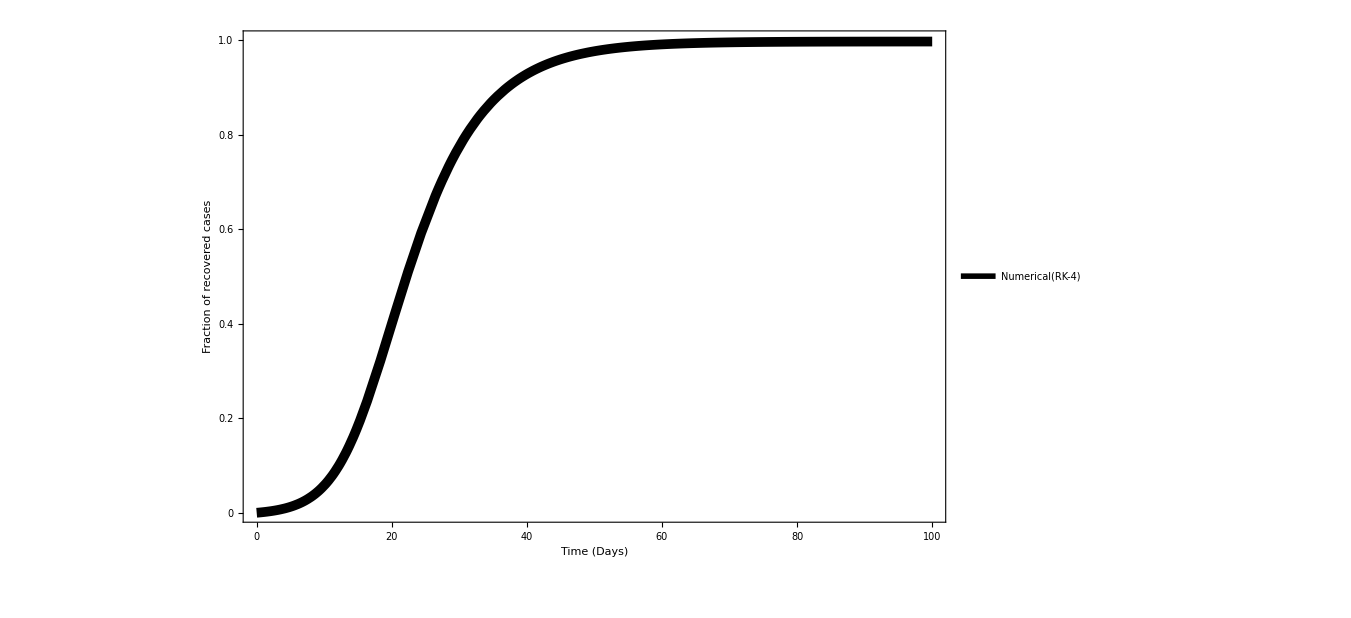

```mathematica
beta=0.75; gamma=1/8; sigma=1/3;I0=0.01; S0=0.98; E0=0.01; R0=0;
Sol1=NDSolve[{S1'[t]==-beta*S1[t]*I1[t],
E1'[t]==beta*S1[t]*I1[t]-sigma*E1[t],
I1'[t]== sigma*E1[t]-gamma*I1[t],
R1'[t]== gamma*I1[t],
S1[0]==0.98,E1[0]==0.01,I1[0]==0.01,R1[0]==0},{S1,E1,I1,R1},{t,0,100}];
P0=Plot[{R1[t]/.Sol1},{t,0,100},PlotRange->{0,1},
PlotStyle->Directive[Black,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->28], Style["Fraction of recovered cases",Bold,Black,FontSize->28]},
PlotLegends-> Placed[LineLegend[{Directive[AbsoluteThickness[5]]},{Style["Numerical(RK-4)",Bold,Black,FontSize->32]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,36],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

```mathematica
f[i_,j_]:=(j)^(i-1);
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

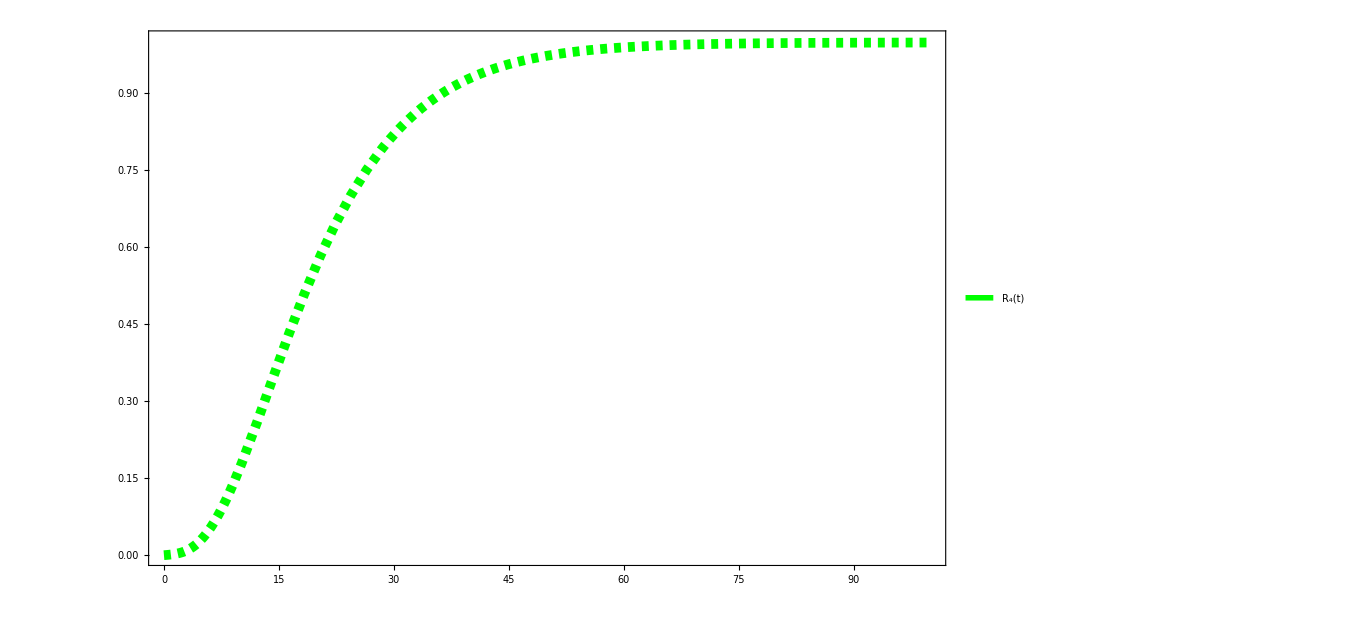

```mathematica
Mn=Table[f[i,j],{i,4},{j,4}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,4-1}];
Soln=Inverse[Mn].Nn;
R4[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,4}];
PR4=Plot[R4[x],{x,0,100},PlotRange->{0,1},
PlotStyle->{Green,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Green,Dashed,AbsoluteThickness[5]]},{Style["R_4(t)",Bold,Italic,Green,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

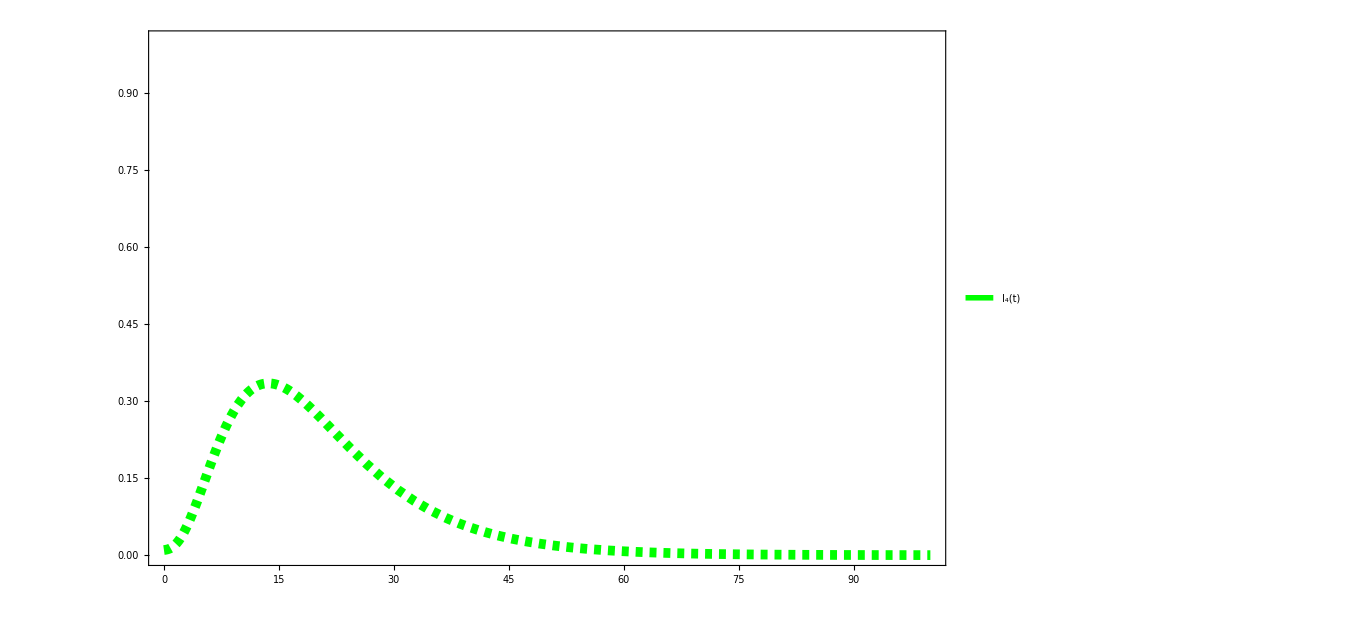

```mathematica
I4=(1/gamma)*D[R4[x],x];
PI4=Plot[I4,{x,0,100},PlotRange->{0,1},
PlotStyle->{Green,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Green,Dashed,AbsoluteThickness[5]]},{Style["I_4(t)",Bold,Italic,Green,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

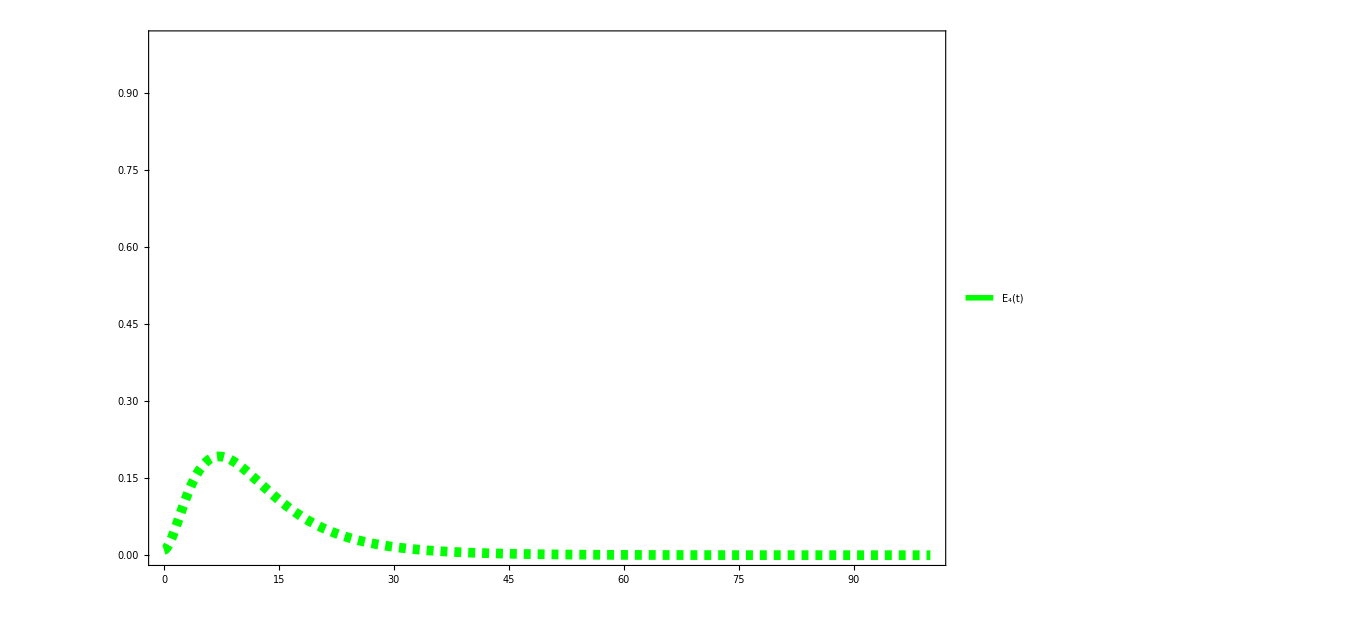

```mathematica
E4=(1/sigma)*(gamma*I4 +D[I4,x]);
PE4=Plot[E4,{x,0,100},PlotRange->{0,1},
PlotStyle->{Green,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Green,Dashed,AbsoluteThickness[5]]},{Style["E_4(t)",Bold,Italic,Green,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

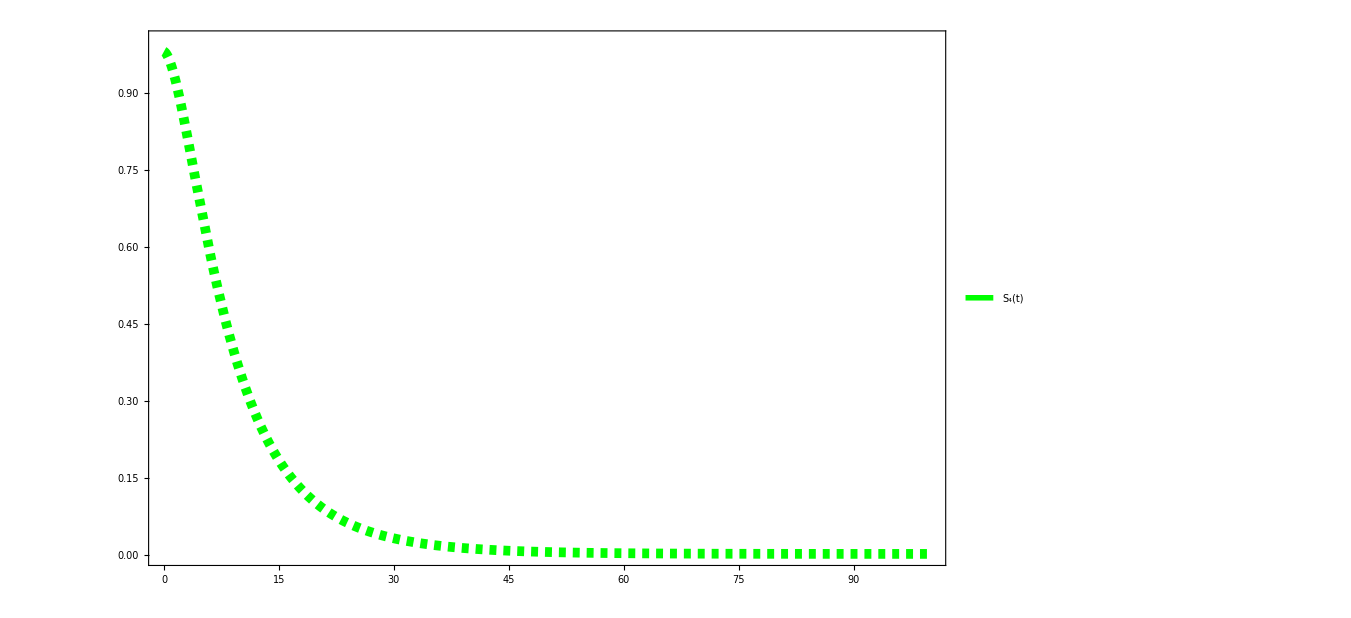

```mathematica
S4=1-E4-I4-R4[x];
PS4=Plot[S4,{x,0,100},PlotRange->{0,1},
PlotStyle->{Green,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Green,Dashed,AbsoluteThickness[5]]},{Style["S_4(t)",Bold,Italic,Green,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

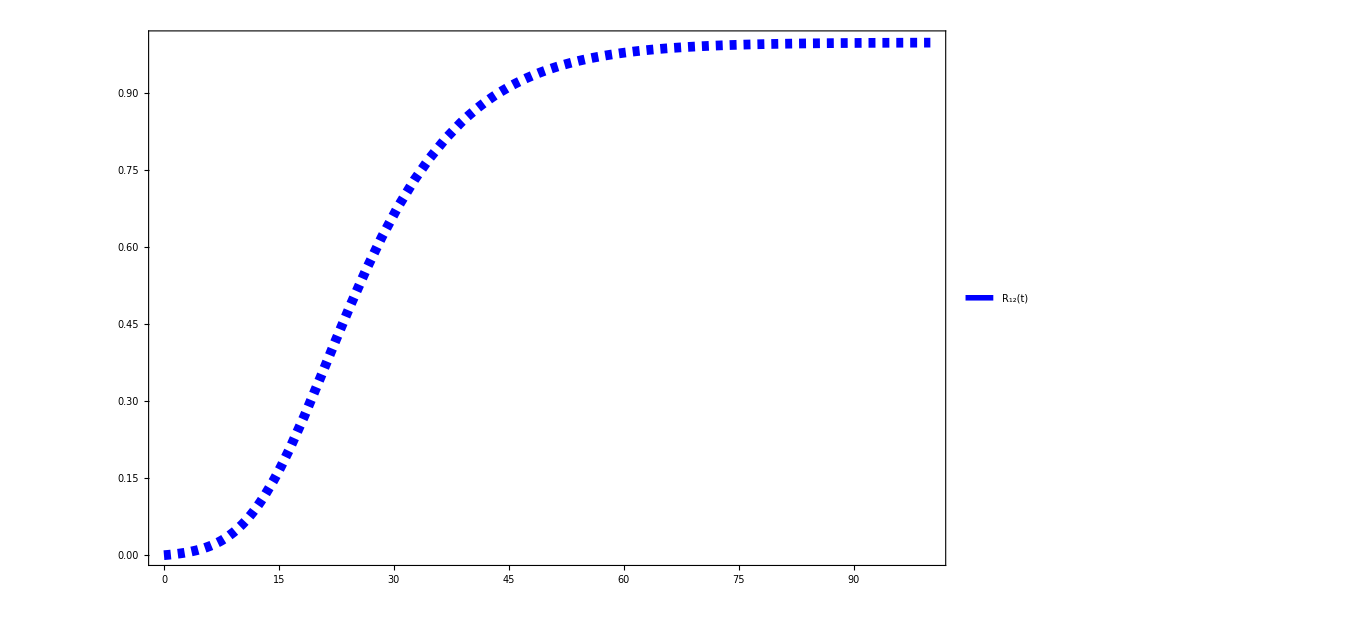

```mathematica
Mn=Table[f[i,j],{i,12},{j,12}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,12-1}];
Soln=Inverse[Mn].Nn;
R12[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,12}];
PR12=Plot[R12[x],{x,0,100},PlotRange->{0,1},
PlotStyle->{Blue,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Blue,Dashed,AbsoluteThickness[5]]},{Style["R_12(t)",Bold,Italic,Blue,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

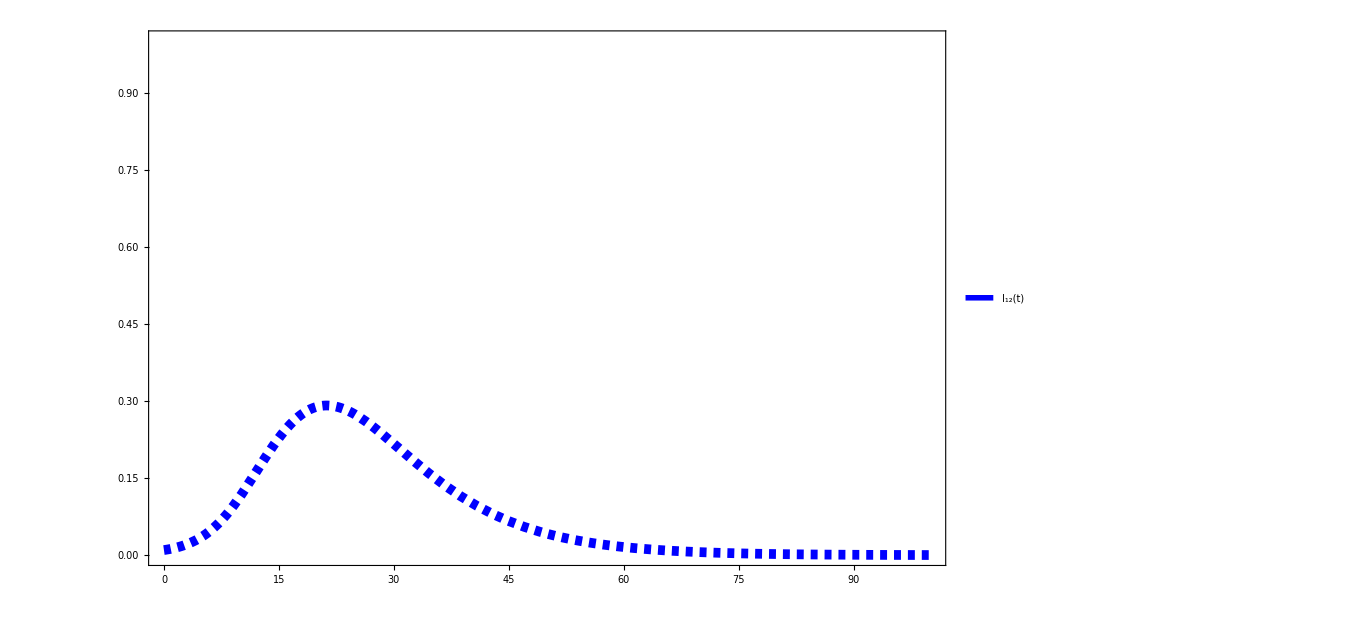

```mathematica
I12=(1/gamma)*D[R12[x],x];
PI12=Plot[I12,{x,0,100},PlotRange->{0,1},
PlotStyle->{Blue,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Blue,Dashed,AbsoluteThickness[5]]},{Style["I_12(t)",Bold,Italic,Blue,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

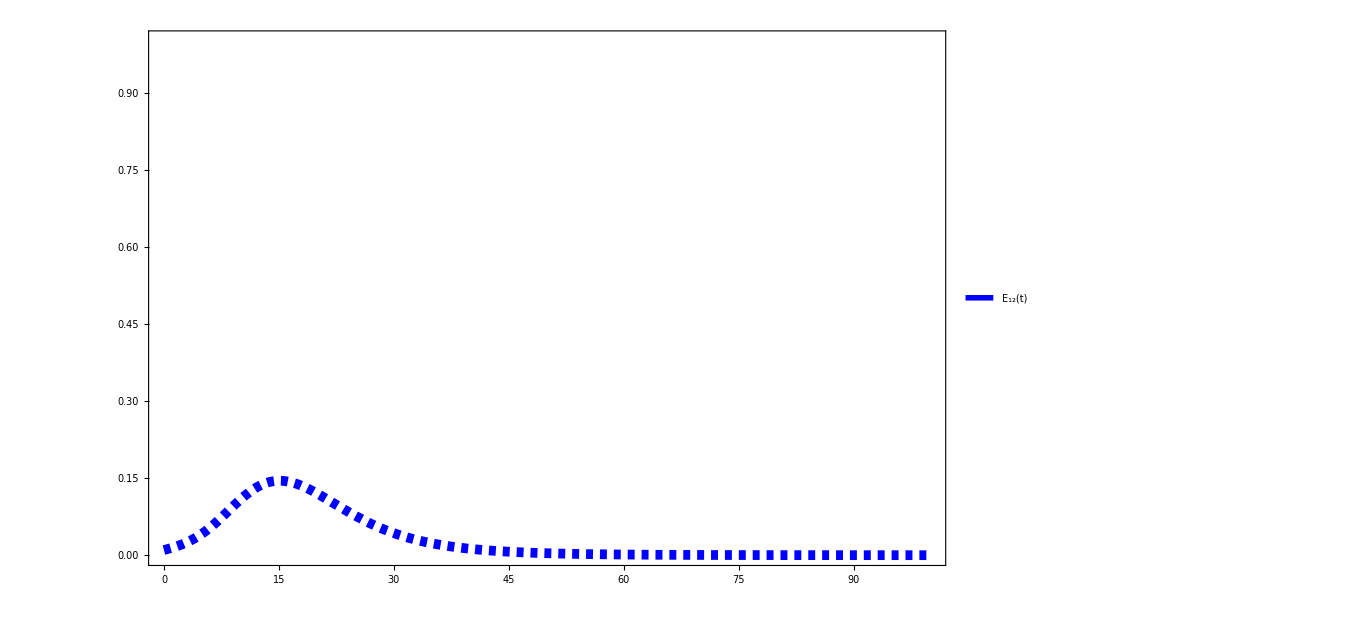

```mathematica
E12=(1/sigma)*(gamma*I12 +D[I12,x]);
PE12=Plot[E12,{x,0,100},PlotRange->{0,1},
PlotStyle->{Blue,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Blue,Dashed,AbsoluteThickness[5]]},{Style["E_12(t)",Bold,Italic,Blue,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

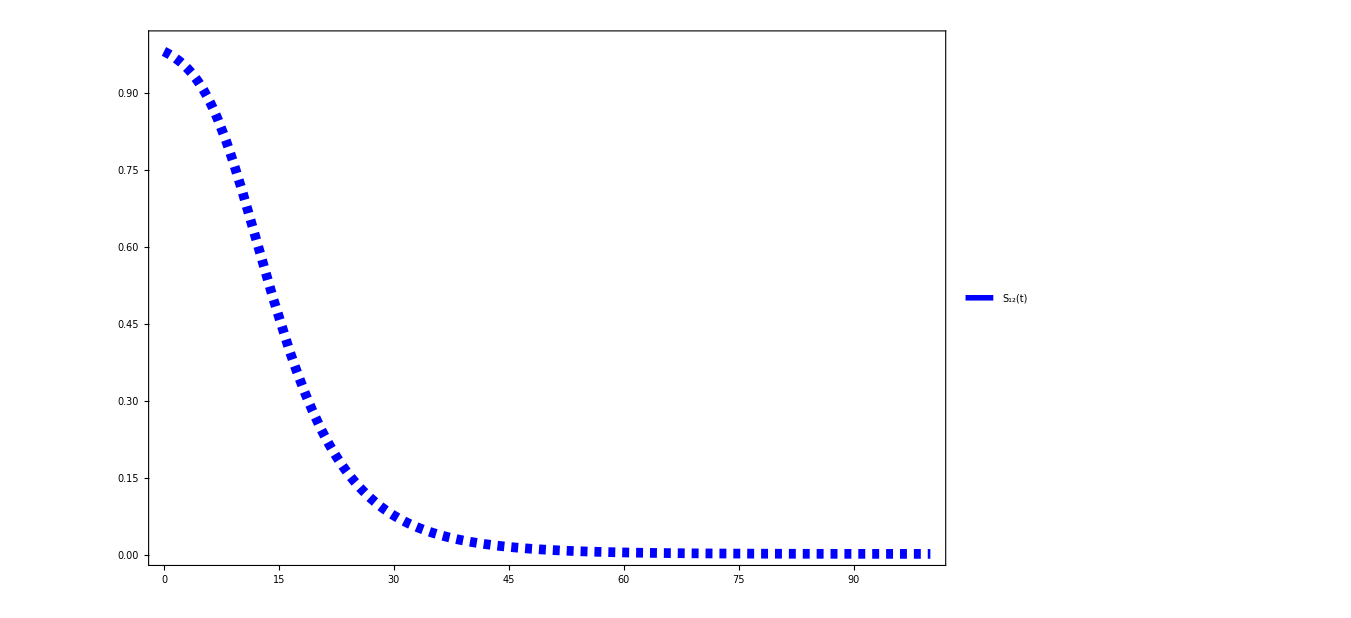

```mathematica
S12=1-E12-I12-R12[x];
PS12=Plot[S12,{x,0,100},PlotRange->{0,1},
PlotStyle->{Blue,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Blue,Dashed,AbsoluteThickness[5]]},{Style["S_12(t)",Bold,Italic,Blue,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

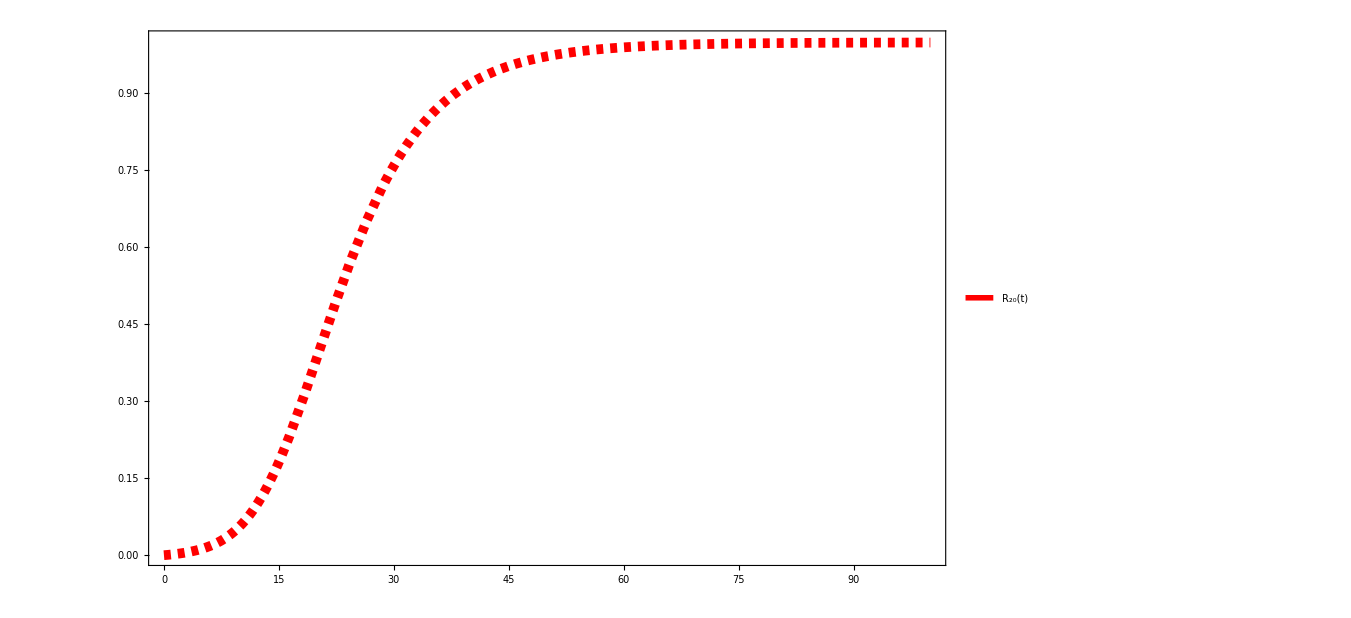

```mathematica
Mn=Table[f[i,j],{i,20},{j,20}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,20-1}];
Soln=Inverse[Mn].Nn;
R20[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,20}];
PR20=Plot[R20[x],{x,0,100},PlotRange->{0,1},
PlotStyle->{Red,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Red,Dashed,AbsoluteThickness[5]]},{Style["R_20(t)",Bold,Italic,Red,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

```mathematica
R20[t]
```

0.997535-0.906981 ⅇ^(-2. t)+18.0889 ⅇ^(-1.9 t)-171.28 ⅇ^(-1.8 t)+1023.69 ⅇ^(-1.7 t)-4330.52 ⅇ^(-1.6 t)+13780.6 ⅇ^(-1.5 t)-34219. ⅇ^(-1.4 t)+67872.2 ⅇ^(-1.3 t)-109161. ⅇ^(-1.2 t)+143670. ⅇ^(-1.1 t)-155430. ⅇ^(-1. t)+138262. ⅇ^(-0.9 t)-100721. ⅇ^(-0.8 t)+59540.1 ⅇ^(-0.7 t)-28099.4 ⅇ^(-0.6 t)+10297. ⅇ^(-0.5 t)-2786.09 ⅇ^(-0.4 t)+499.369 ⅇ^(-0.3 t)-40.602 ⅇ^(-0.2 t)-3.74085 ⅇ^(-0.1 t)

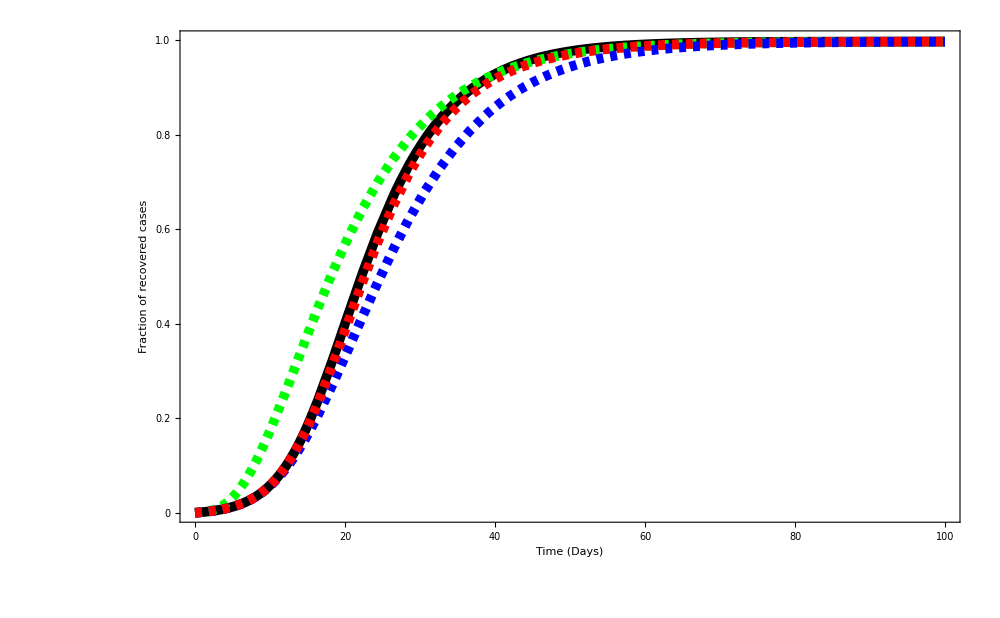

```mathematica
Show[P0,PR4,PR12,PR20]
```

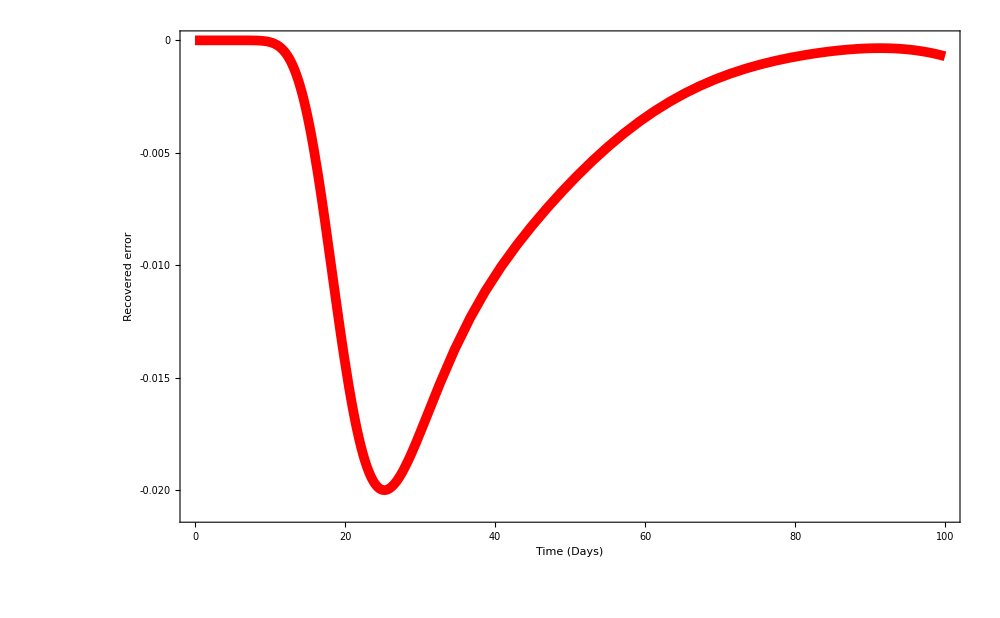

```mathematica
Plot[R20[x]-R1[x]/.Sol1,{x,0,100},
PlotRange->{-0.021,0},
PlotStyle->Directive[Red,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->32], Style["Recovered error",Bold,Black,FontSize->32]},
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,32],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

```mathematica
Sum[(R20[x]-R1[x]/.Sol1)^2,{x,0,100}]/101
```

{0.0000675307}

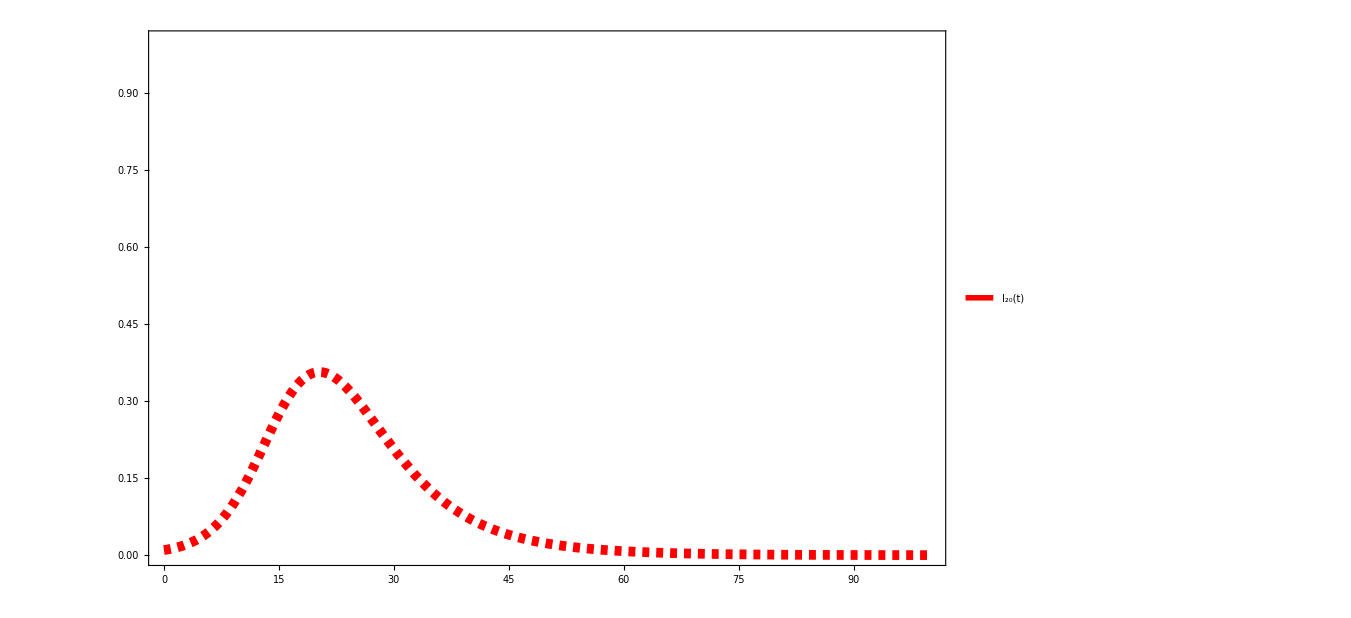

```mathematica
I20=(1/gamma)*D[R20[x],x];
PI20=Plot[I20,{x,0,100},PlotRange->{0,1},
PlotStyle->{Red,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Red,Dashed,AbsoluteThickness[5]]},{Style["I_20(t)",Bold,Italic,Red,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

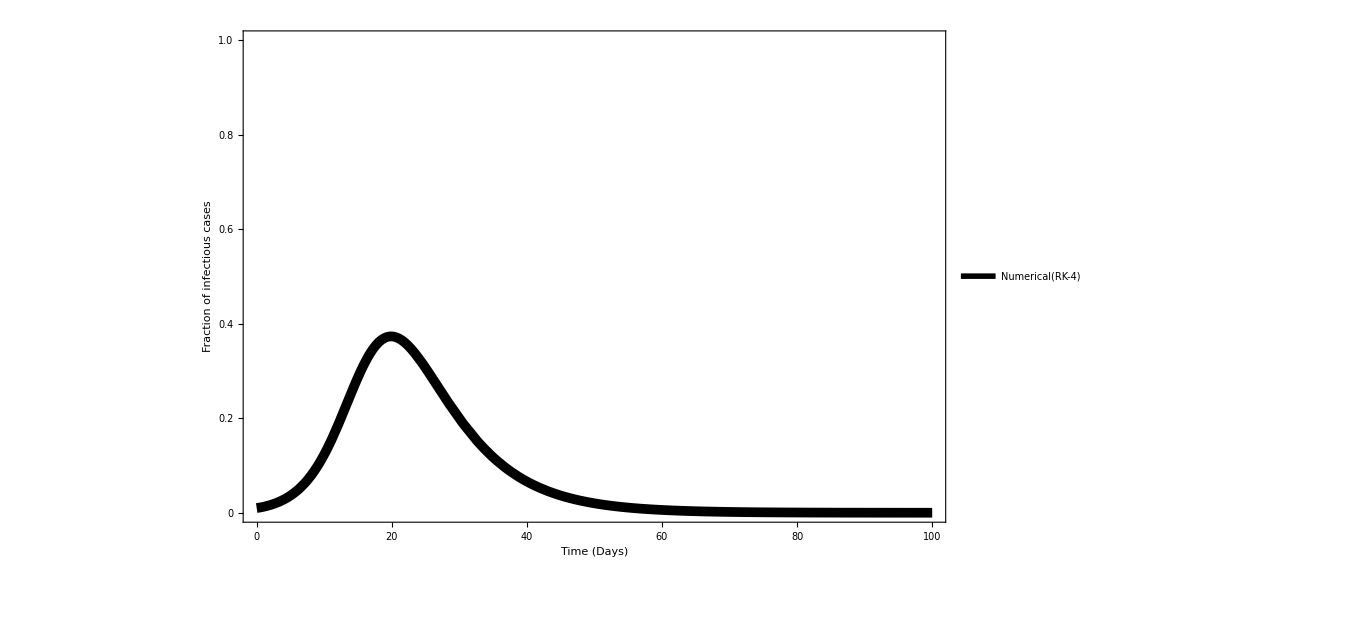

```mathematica
Sol1=NDSolve[{S1'[t]==-beta*S1[t]*I1[t],
E1'[t]==beta*S1[t]*I1[t]-sigma*E1[t],
I1'[t]== sigma*E1[t]-gamma*I1[t],
R1'[t]== gamma*I1[t],
S1[0]==0.98,E1[0]==0.01,I1[0]==0.01,R1[0]==0},{S1,E1,I1,R1},{t,0,100}];
PI0=Plot[{I1[t]/.Sol1},{t,0,100},PlotRange->{0,1},
PlotStyle->Directive[Black,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->28], Style["Fraction of infectious cases",Bold,Black,FontSize->28]},
PlotLegends-> Placed[LineLegend[{Directive[AbsoluteThickness[5]]},{Style["Numerical(RK-4)",Bold,Black,FontSize->32]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,36],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

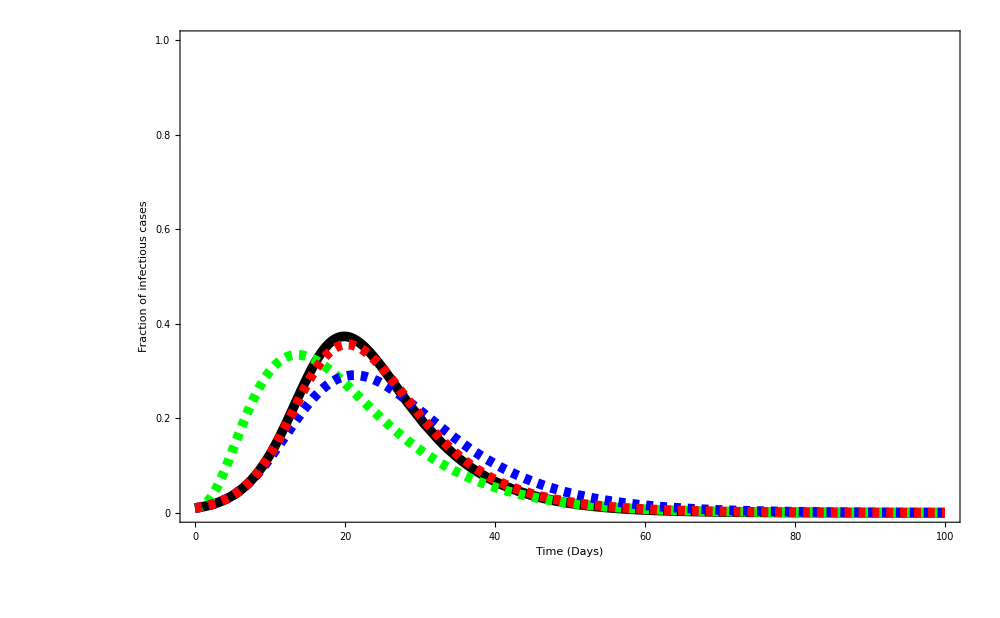

```mathematica
Show[PI0,PI4,PI12,PI20]
```

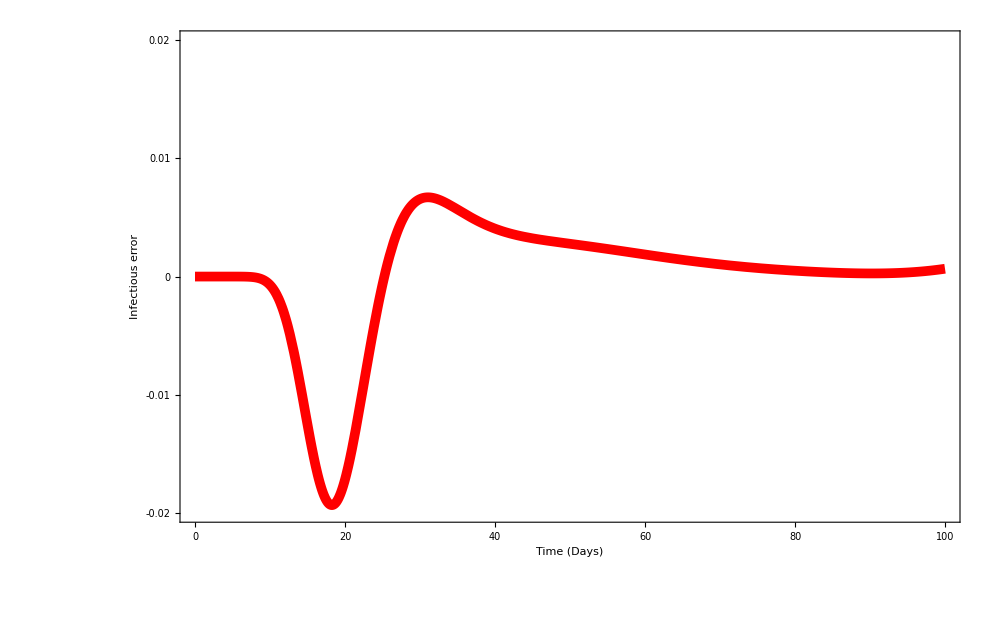

```mathematica
Plot[I20-I1[x]/.Sol1,{x,0,100},PlotRange->{-0.02,0.02},
PlotStyle->Directive[Red,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->32], Style["Infectious error",Bold,Black,FontSize->32]},
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,32],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

```mathematica
Sum[(I20-I1[x]/.Sol1)^2,{x,0,100}]/101
```

{0.0000287791}

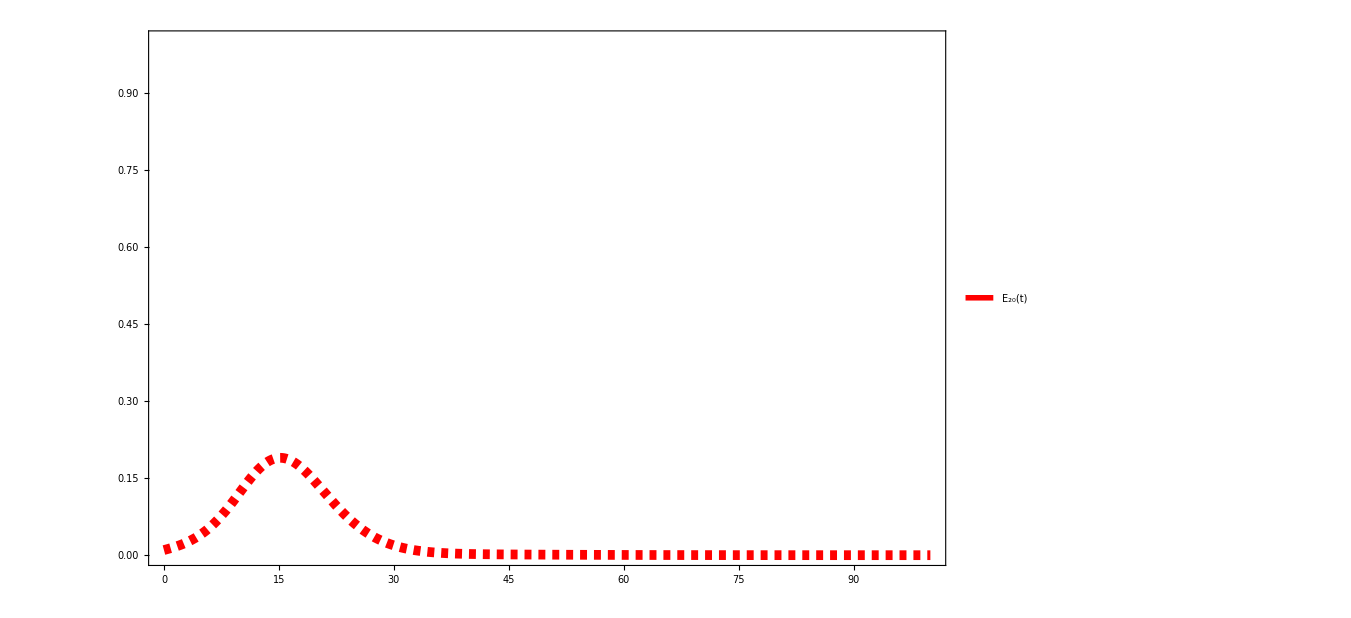

```mathematica
E20=(1/sigma)*(gamma*I20 +D[I20,x]);
PE20=Plot[E20,{x,0,100},PlotRange->{0,1},
PlotStyle->{Red,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Red,Dashed,AbsoluteThickness[5]]},{Style["E_20(t)",Bold,Italic,Red,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

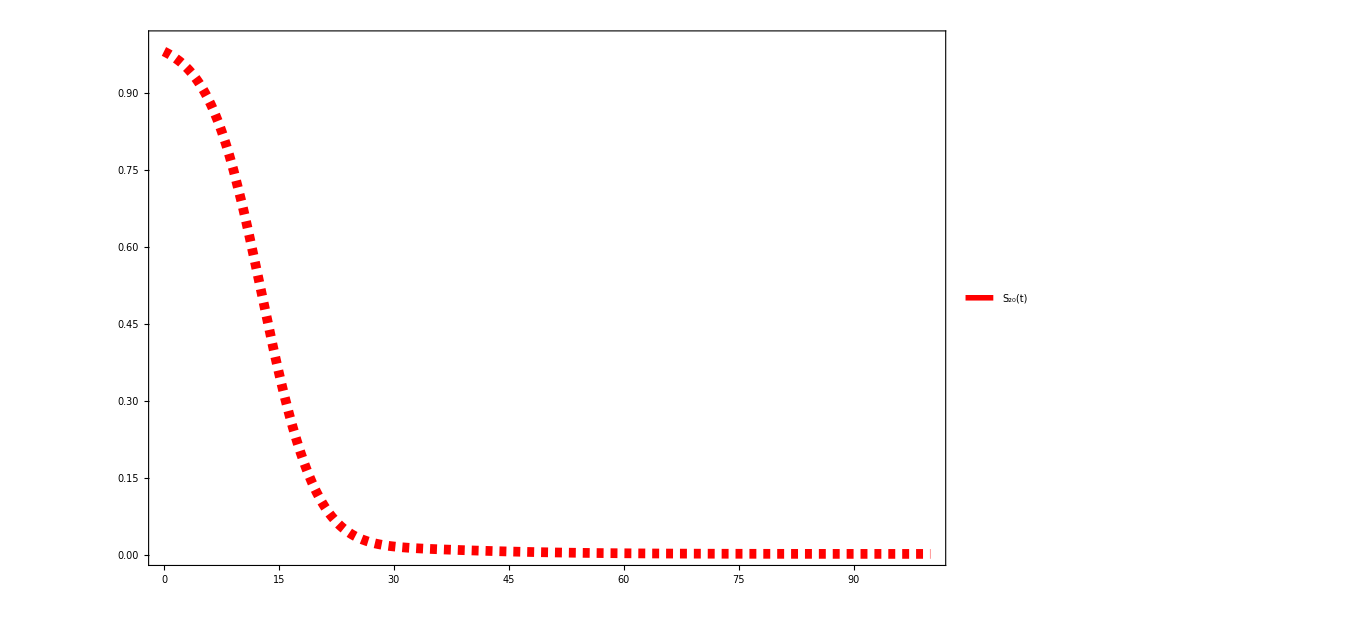

```mathematica
S20=1-E20-I20-R20[x];
PS20=Plot[S20,{x,0,100},PlotRange->{0,1},
PlotStyle->{Red,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Red,Dashed,AbsoluteThickness[5]]},{Style["S_20(t)",Bold,Italic,Red,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

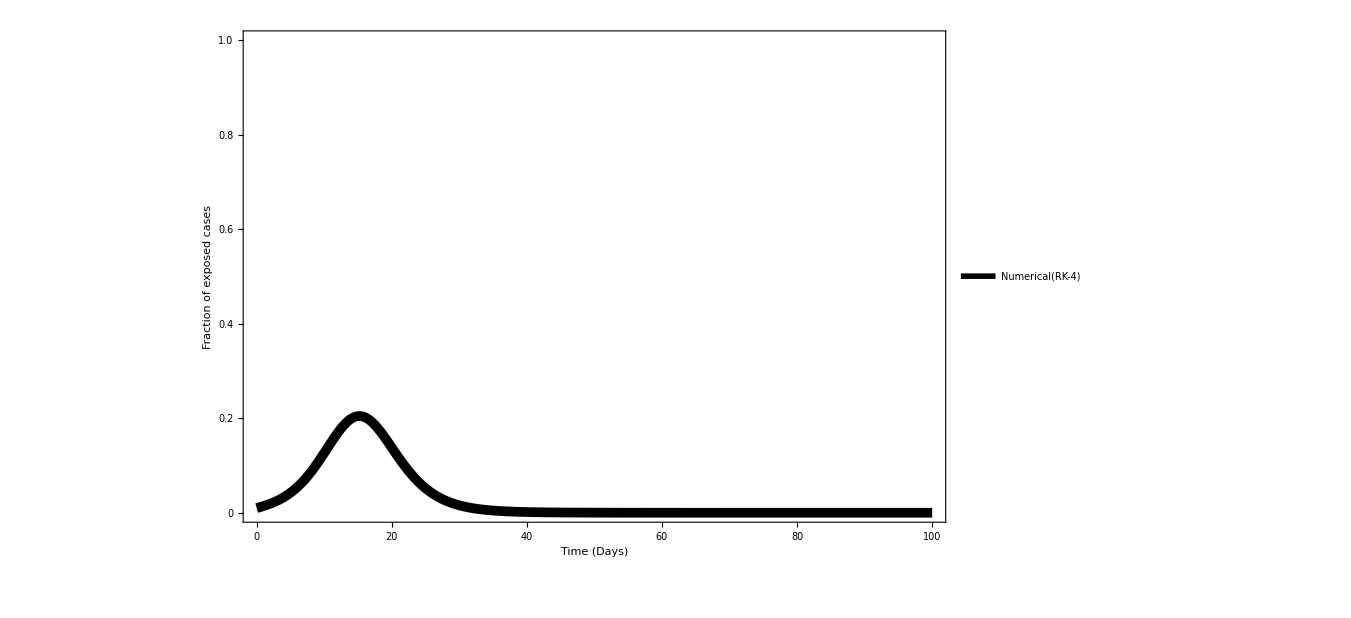

```mathematica
Sol1=NDSolve[{S1'[t]==-beta*S1[t]*I1[t],
E1'[t]==beta*S1[t]*I1[t]-sigma*E1[t],
I1'[t]== sigma*E1[t]-gamma*I1[t],
R1'[t]== gamma*I1[t],
S1[0]==0.98,E1[0]==0.01,I1[0]==0.01,R1[0]==0},{S1,E1,I1,R1},{t,0,100}];
PE0=Plot[{E1[t]/.Sol1},{t,0,100},PlotRange->{0,1},
PlotStyle->Directive[Black,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->28], Style["Fraction of exposed cases",Bold,Black,FontSize->28]},
PlotLegends-> Placed[LineLegend[{Directive[AbsoluteThickness[5]]},{Style["Numerical(RK-4)",Bold,Black,FontSize->32]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,36],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

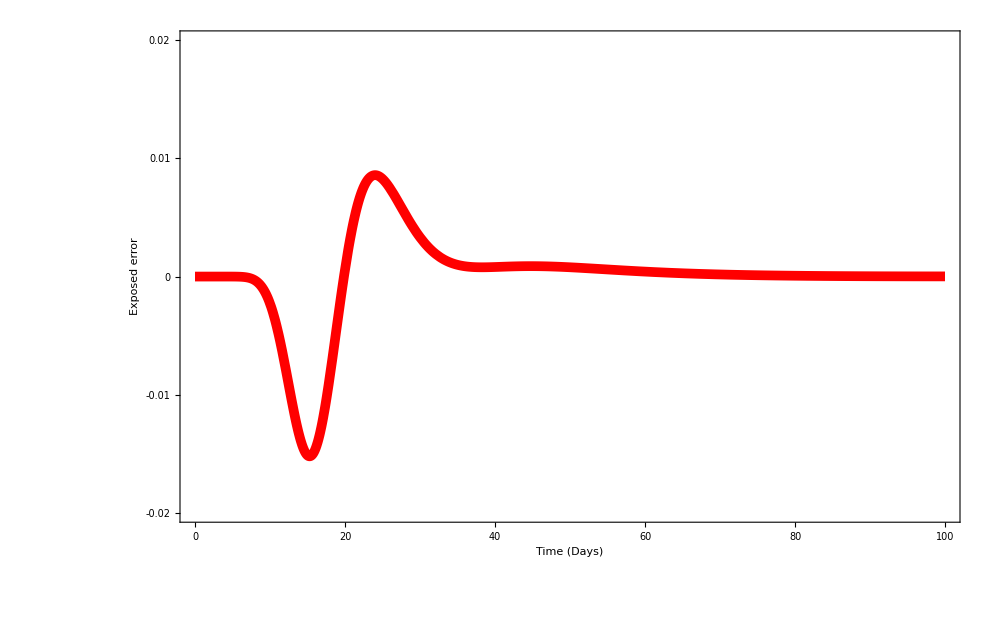

```mathematica
Plot[E20-E1[x]/.Sol1,{x,0,100},PlotRange->{-0.02,0.02},
PlotStyle->Directive[Red,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->32], Style["Exposed error",Bold,Black,FontSize->32]},
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,32],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

```mathematica
Sum[(E20-E1[x]/.Sol1)^2,{x,0,100}]/101
```

{0.0000150904}

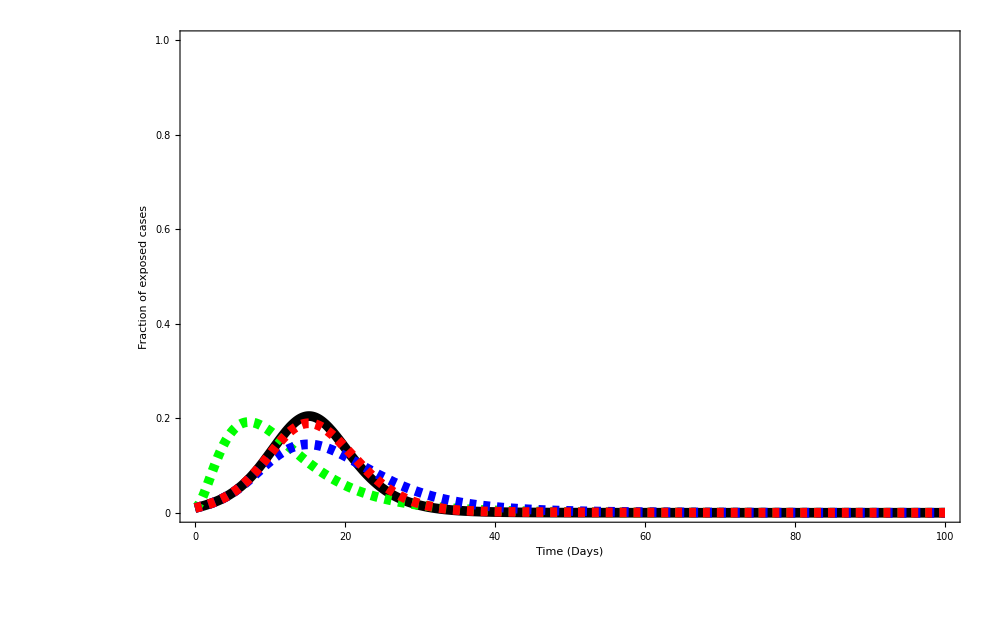

```mathematica
Show[PE0,PE4,PE12,PE20]
```

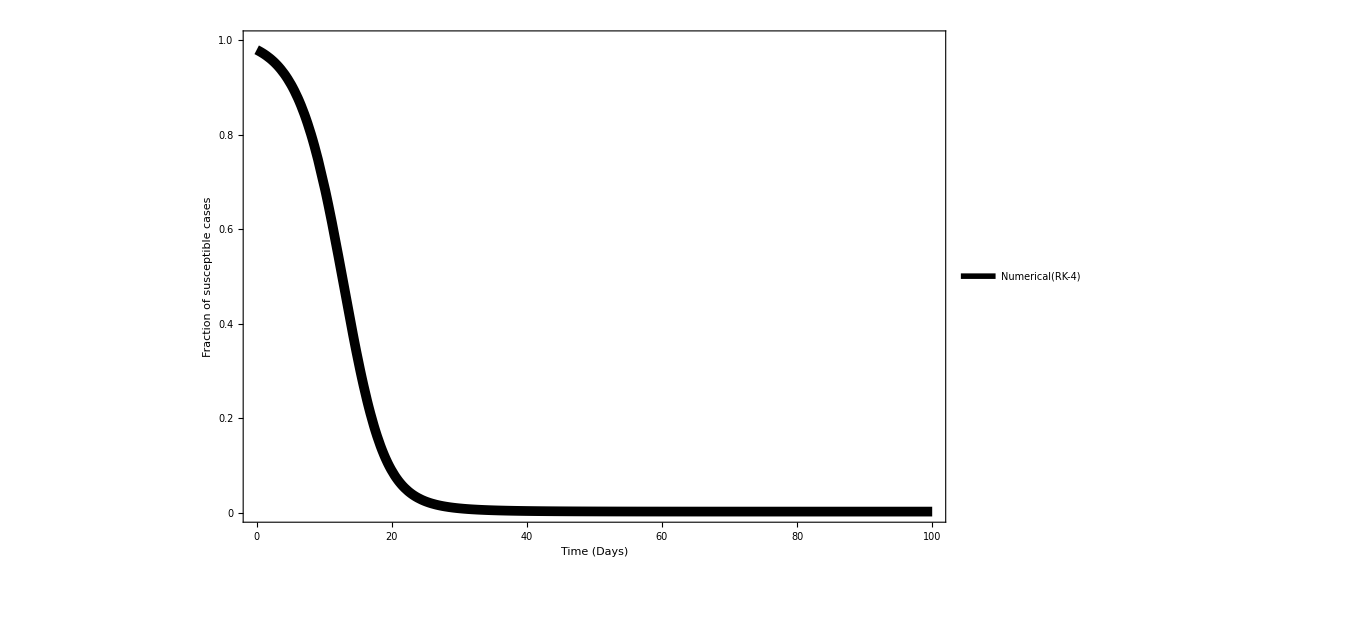

```mathematica
Sol1=NDSolve[{S1'[t]==-beta*S1[t]*I1[t],
E1'[t]==beta*S1[t]*I1[t]-sigma*E1[t],
I1'[t]== sigma*E1[t]-gamma*I1[t],
R1'[t]== gamma*I1[t],
S1[0]==0.98,E1[0]==0.01,I1[0]==0.01,R1[0]==0},{S1,E1,I1,R1},{t,0,100}];
PS0=Plot[{S1[t]/.Sol1},{t,0,100},PlotRange->{0,1},
PlotStyle->Directive[Black,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->28], Style["Fraction of susceptible cases",Bold,Black,FontSize->28]},
PlotLegends-> Placed[LineLegend[{Directive[AbsoluteThickness[5]]},{Style["Numerical(RK-4)",Bold,Black,FontSize->32]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,36],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

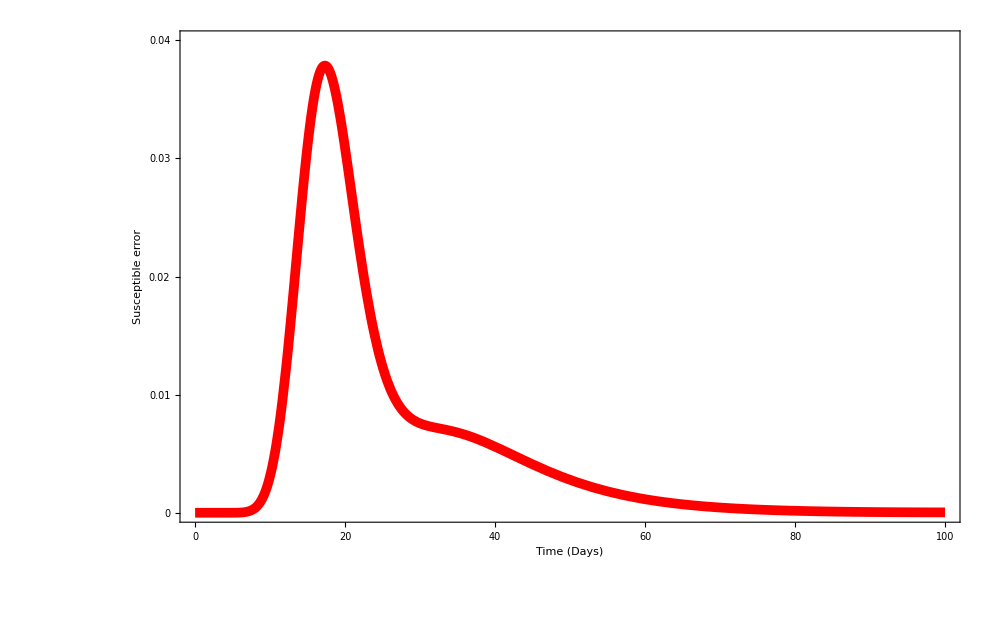

```mathematica
Plot[S20-S1[x]/.Sol1,{x,0,100},PlotRange->{0,0.04},
PlotStyle->Directive[Red,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->32], Style["Susceptible error",Bold,Black,FontSize->32]},
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,32],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

```mathematica
Sum[(S20-S1[x]/.Sol1)^2,{x,0,100}]/101
```

{0.000111401}

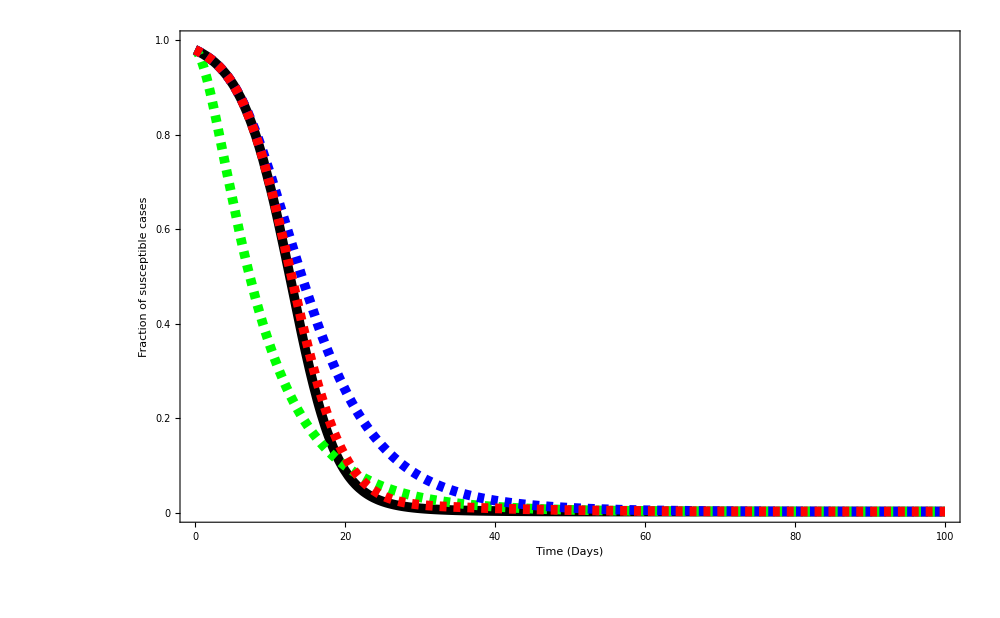

```mathematica
Show[PS0,PS4,PS12,PS20]
```

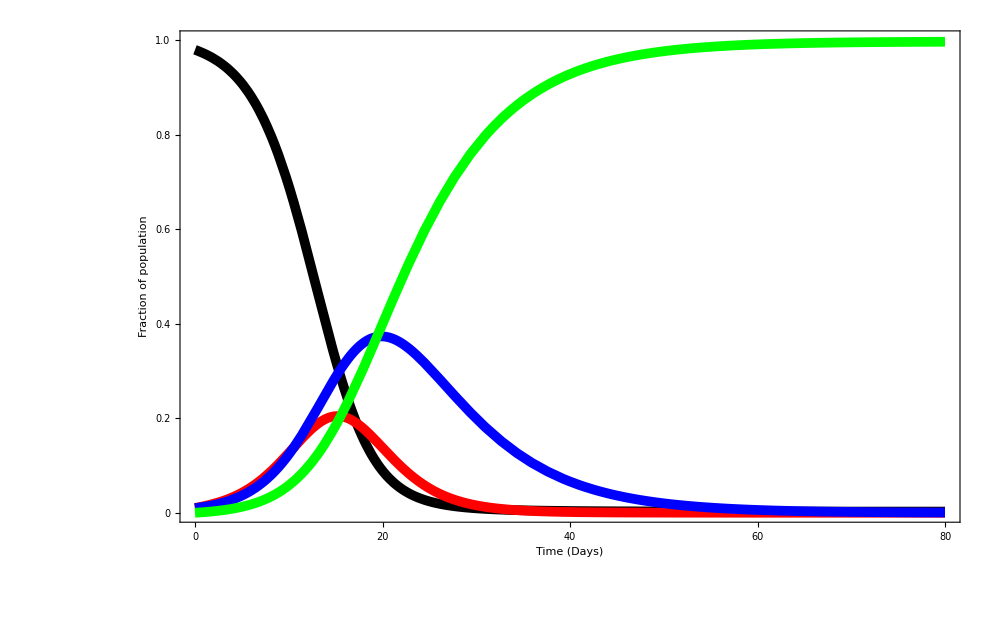

```mathematica
Sol1=NDSolve[{S1'[t]==-beta*S1[t]*I1[t],
E1'[t]==beta*S1[t]*I1[t]-sigma*E1[t],
I1'[t]== sigma*E1[t]-gamma*I1[t],
R1'[t]== gamma*I1[t],
S1[0]==0.98,E1[0]==0.01,I1[0]==0.01,R1[0]==0},{S1,E1,I1,R1},{t,0,80}];
PSS0=Plot[{S1[t]/.Sol1},{t,0,80},PlotRange->{0,1},
PlotStyle->Directive[Black,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->28], Style["Fraction of population",Bold,Black,FontSize->28]},
PlotLegends-> Placed[LineLegend[{Directive[AbsoluteThickness[5]]},{Style["Susceptible(RK-4)",Bold,Black,FontSize->32]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,36],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000];
PEE0=Plot[{E1[t]/.Sol1},{t,0,80},PlotRange->{0,1},
PlotStyle->Directive[Red,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->28], Style["Fraction of population",Bold,Black,FontSize->28]},
PlotLegends-> Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]]},{Style["Exposed(RK-4)",Bold,Black,FontSize->32]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,36],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000];
PII0=Plot[{I1[t]/.Sol1},{t,0,80},PlotRange->{0,1},
PlotStyle->Directive[Blue,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->28], Style["Fraction of population",Bold,Black,FontSize->28]},
PlotLegends-> Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]]},{Style["Infectious(RK-4)",Bold,Black,FontSize->32]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,36],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000];
PRR0=Plot[{R1[t]/.Sol1},{t,0,80},PlotRange->{0,1},
PlotStyle->Directive[Green,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->28], Style["Fraction of population",Bold,Black,FontSize->28]},
PlotLegends-> Placed[LineLegend[{Directive[Green,AbsoluteThickness[5]]},{Style["Recovered(RK-4)",Bold,Black,FontSize->32]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,36],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000];
Show[PSS0,PEE0,PII0,PRR0]
```

```mathematica
Mn=Table[f[i,j],{i,20},{j,20}];
SolRty=Solve[x+(gamma/beta)*Log[(1-x)/S0 ]==0&&0<=x≤1,x];
Rfty=x/.SolRty;
e[0]=E0;s[0]=S0;i[0]=I0;
s[1]=-beta*i[0]*s[0];
s[n_]:=-beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}];
i[n_]:=sigma*e[n-1]-gamma*i[n-1];
e[n_]:=beta*Sum[Binomial[n-1,k]i[n-1-k]*s[k],{k,0,n-1}]-sigma*e[n-1];
d[-2]=-Rfty[[1]];
d[-1]=gamma*I0;
d[n_]:=gamma*(sigma*e[n]-gamma*i[n]);
F[n_]:=(-1)^(n)*d[n-2]/Lam1^(n);
Lam1=0.1;
Nn=Table[F[n],{n,0,20-1}];
Soln=Inverse[Mn].Nn;
R20[x_]:=-d[-2]+Sum[Soln[[i]]*Exp[-(i)*Lam1*x],{i,20}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
PR20=Plot[R20[x],{x,0,100},PlotRange->{0,1},
PlotStyle->{Black,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Black,Dashed,AbsoluteThickness[5]]},{Style["R_20(t)",Bold,Italic,Black,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000];
I20=(1/gamma)*D[R20[x],x];
PI20=Plot[I20,{x,0,100},PlotRange->{0,1},
PlotStyle->{Orange,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Orange,Dashed,AbsoluteThickness[5]]},{Style["I_20(t)",Bold,Italic,Black,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000];
E20=(1/sigma)*(gamma*I20 +D[I20,x]);
PE20=Plot[E20,{x,0,100},PlotRange->{0,1},
PlotStyle->{Brown,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Brown,Dashed,AbsoluteThickness[5]]},{Style["E_20(t)",Bold,Italic,Black,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000];
S20=1-E20-I20-R20[x];
PS20=Plot[S20,{x,0,100},PlotRange->{0,1},
PlotStyle->{Yellow,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Yellow,Dashed,AbsoluteThickness[5]]},{Style["S_20(t)",Bold,Italic,Black,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000];
```

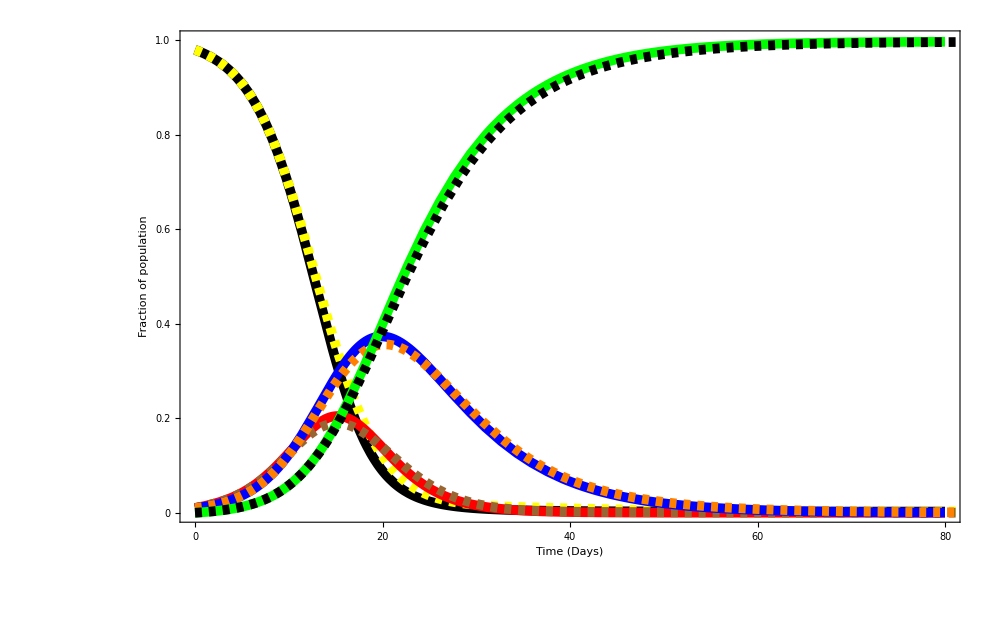

```mathematica
Show[PSS0,PS20,PEE0,PE20,PII0,PI20,PRR0,PR20]
```